Exercises for Section 21 | Graphs and Networks

Make a graph consisting of a loop of 3 nodes. |

EXPECTED OUTPUT »

-Graphics- | ×



```mathematica
Graph[{1->2,2->3,3->1}]
```

Make a graph with 4 nodes in which every node is connected. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Graph[Flatten[Table[i->j,{i,4},{j,4}]]]
```

-Graphics-

Make a table of undirected graphs with between 2 and 10 nodes in which every node is connected. |

EXPECTED OUTPUT »

-Graphics- | ×

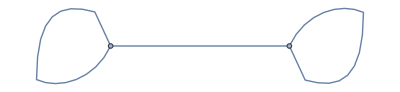
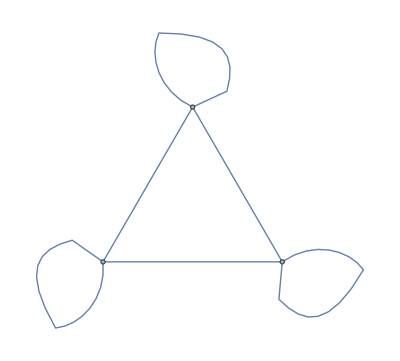
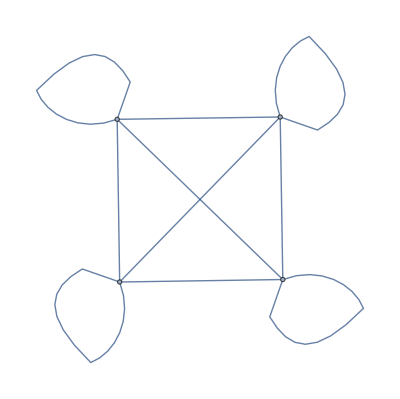
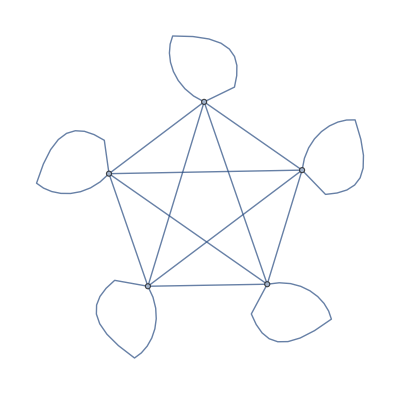
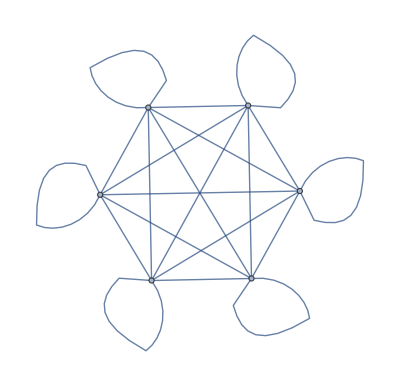
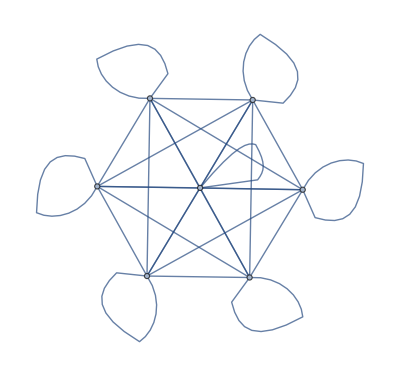
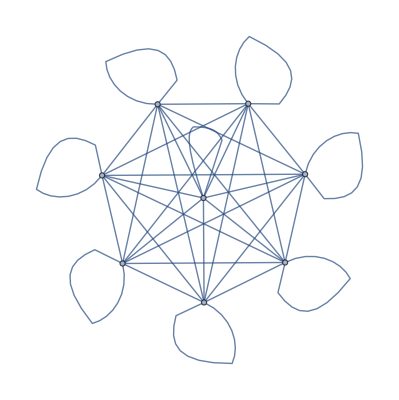
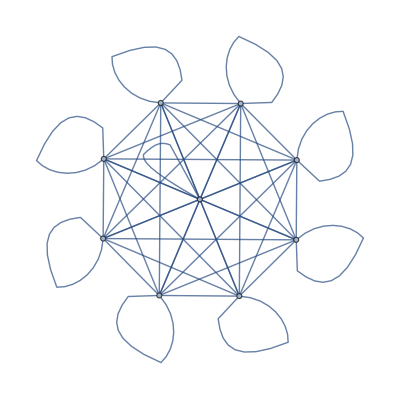

```mathematica
Table[UndirectedGraph[Flatten[Table[i->j,{i,n},{j,n}]]],{n,2,10,1}]
```

Use Table and Flatten to get {1,2,1,2,1,2}. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Flatten[Table[{1,2},3]]
```

{1,2,1,2,1,2}

Make a line plot of the result of concatenating all digits of all integers from 1 to 100 (i.e. ..., 8, 9, 1, 0, 1, 1, 1, 2, ...). |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ListLinePlot[Flatten[IntegerDigits[Range[100]]]]
```

-Graphics-

Make a graph with 50 nodes, in which node i connects to node i+1. |

EXPECTED OUTPUT »

-Graphics- | ×

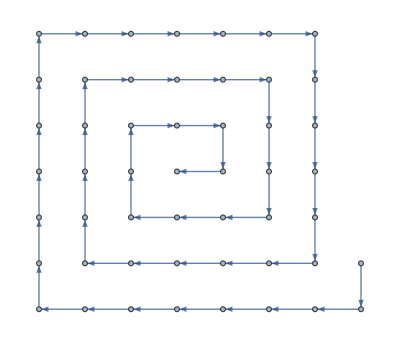

```mathematica
Graph[Table[i->(i+1),{i,50}]]
```

Make a graph with 4 nodes, in which each connection connects i to Max[i,j]. |

EXPECTED OUTPUT »

-Graphics- | ×

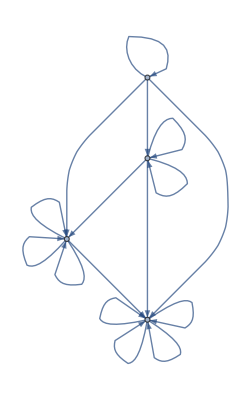

```mathematica
Graph[Flatten[Table[i->(Max[i,j]),{i,4},{j,4}]]]
```

Make a graph in which each connection connects i to j-i, where i and j both range from 1 to 5. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Graph[Flatten[Table[i->(j-i),{i,1,5},{j,1,5}]]]
```

-Graphics-

Generate a graph with 100 nodes, each with a connection going to one randomly chosen node. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Graph[Flatten[Table[i->RandomInteger[{1,100}],{i,100}]]]
```

-Graphics-

Generate a graph with 100 nodes, each connecting to two randomly chosen nodes. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Graph[Flatten[Table[{i->RandomInteger[{1,100}],i->RandomInteger[{1,100}]},{i,100}]]]
```

-Graphics-

For the graph {1→2,2→3,3→4,4→1,3→1,2→2}, make a grid giving the shortest paths between every pair of nodes, with the start node as row and end node as column. |

EXPECTED OUTPUT »

-Graphics- | ×

FindShortestPath::inv: The argument a in FindShortestPath[Graph[<4>, <6>], a, b] is not a valid vertex.

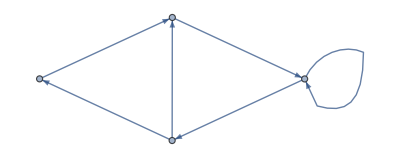
Grid[FindShortestPath[-Graphics-,a,b]]

a | b
c | d

```mathematica
Grid[FindShortestPath[Graph[{1->2,2->3,3->4,4->1,3->1,2->2}],a,b]]
Grid[{{a,b},{c,d}}]
```

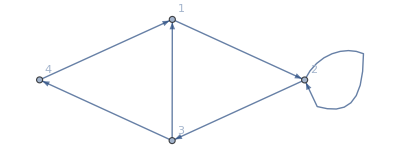

{1} | {1,2} | {1,2,3} | {1,2,3,4}
{2,3,1} | {2} | {2,3} | {2,3,4}
{3,1} | {3,1,2} | {3} | {3,4}
{4,1} | {4,1,2} | {4,1,2,3} | {4}

```mathematica
Graph[{1->2,2->3,3->4,4->1,3->1,2->2},VertexLabels->All]
Grid[Table[FindShortestPath[Graph[{1->2,2->3,3->4,4->1,3->1,2->2}],i,j],{i,1,4},{j,1,4}]]
```

```mathematica
Grid[Table[FindShortestPath[Graph[{1->2,2->3,3->4,4->1,3->1,2->2}],i,j],{i,1,4},{j,1,4}]]
```

{1} | {1,2} | {1,2,3} | {1,2,3,4}
{2,3,1} | {2} | {2,3} | {2,3,4}
{3,1} | {3,1,2} | {3} | {3,4}
{4,1} | {4,1,2} | {4,1,2,3} | {4}

Make a graph with 4 nodes in which every node is connected, displaying the resulting graph with radial drawing. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Graph[Flatten[Table[i->j,{i,4},{j,4}]],GraphLayout->"RadialDrawing"]
```

-Graphics-

Generate a graph in which a single node is connected to 10 others. |

EXPECTED OUTPUT »

-Graphics- | ×

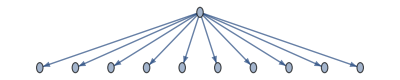

```mathematica
Graph[Flatten[Table[i->j,{j,Range[10]}]]]
```

Use Flatten to generate a table of the numbers 1 to 50 in which even numbers are colored red. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Table[{Style[i,Red],j},{i,10},{j,10}]
```

{{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10}},{{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10}},{{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10}},{{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10}},{{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{5,7},{5,8},{5,9},{5,10}},{{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{6,7},{6,8},{6,9},{6,10}},{{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{7,8},{7,9},{7,10}},{{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8},{8,9},{8,10}},{{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8},{9,9},{9,10}},{{10,1},{10,2},{10,3},{10,4},{10,5},{10,6},{10,7},{10,8},{10,9},{10,10}}}

```mathematica
Table[{Style[i,Red],j},{i,0,10,2},{j,0,10,3}]
```

{{{0,0},{0,3},{0,6},{0,9}},{{2,0},{2,3},{2,6},{2,9}},{{4,0},{4,3},{4,6},{4,9}},{{6,0},{6,3},{6,6},{6,9}},{{8,0},{8,3},{8,6},{8,9}},{{10,0},{10,3},{10,6},{10,9}}}

```mathematica
Flatten[Table[{Style[i,Red],j},25]]
Table[Table[i,{}],{}]
```

{i,j,i,j,i,j,i,j,i,j,i,j,i,j,i,j,i,j,i,j,i,j,i,j,i,j,i,j,i,j,i,j,i,j,i,j,i,j,i,j,i,j,i,j,i,j,i,j,i,j}

```mathematica
Flatten[Table[{n,Style[1+n,Red]},{n,1,50,2}]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50}

Use ImageData, Flatten and Total to find the number of white pixels in Binarize[Rasterize["W"]]. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Total[Flatten[ImageData[Binarize[Rasterize["W"]]]],1]
```

98

Use Flatten, IntegerDigits and Total to find the sum of all digits of all whole numbers up to 1000. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Total[Flatten[Table[IntegerDigits[n],{n,1,1000,1}]]]
```

13501

Generate a graph with 200 connections, each between nodes with numbers randomly chosen between 0 and 100. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Graph[Table[RandomInteger[100]->RandomInteger[100],200]]
```

-Graphics-

Generate a plot that shows communities in a random graph with nodes numbered between 0 and 100, and 200 connections. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
CommunityGraphPlot[Graph[Table[RandomInteger[100]->RandomInteger[100],200]]]
```

-Graphics-